# Direct Detection

```mathematica
Clear[dsigma]
Z = 54;
A=129;
JA = 3/2;
Rc = 1.14*A^(1/3)*5*^3;
Rs = 1.0*A^(1/3)*5*^3;
muA=0.691;
mA = A;
e=Sqrt[4Pi/128];
aem = 1/128;
gl2f = 1;
sw2 = 0.23122;
GF = 1.166*^-5;
Ncq = 3;
Ncl = 1;
mqdiff = 800;
mChif = 100;
muRed = mChif*mA/(mChif+mA);
v = 230*^3/(3*^8);
ERmax = 2.0mA mChif v^2 /(mChif + mA);
epsb = 4/mChif;
Clear[mu]
```

```mathematica
mu[mPhi_,mChi_]:= mPhi^2/mChi^ 2
eps[mf_,mChi_]:= mf^2/mChi^ 2
Delta[mu_,eps_]:= mu^ 2+(eps-1)^2-2mu(eps+1)
fpTree[g_,mPhi_,mChi_]:= 3g^2/(8(mPhi^ 2-mChi ^2))
fnTree[g_,mPhi_,mChi_]:= 3g^2/(8(mPhi^ 2-mChi ^2))
muChi[Qf_,Nc_,g_,mChi_,Delta_,mu_,eps_] := -Qf*e*Nc*g^2/(32Pi^ 2mChi)*((-Delta+1-mu-eps)/Sqrt[Delta]*ArcTanh[Sqrt[Delta]/(mu+eps-1)] + 1/2(eps-mu)Log[eps/mu]-1);
bChi[Qf_,Nc_,g_,mChi_,Delta_,mu_,eps_]:=-Qf e Nc g^2/(384Pi^ 2mChi^ 2)*(2/Delta^ (3/2)(8Delta^ 2+(9mu+7eps-5)Delta - 4eps(3mu+eps-1))ArcTanh[Sqrt[Delta]/(mu+eps-1)] + (8mu-8eps+1)Log[eps/mu] + 4(4+(mu+3eps-1)/Delta));
azR[T3_,Nc_,g_,Delta_,mu_,eps_]:= T3*Nc*g^2*eps/(16Pi^2) * (1/2 Log[eps/mu]+(1+mu-eps)/Sqrt[Delta] ArcTanh[Sqrt[Delta]/(mu+eps-1)]);
az = -azR[0.5,3,gl2f,Delta[mu[mChif+mqdiff,mChif],1],mu[mChif+mqdiff,mChif],1]-azR[-0.5,3,gl2f,Delta[mu[mChif+mqdiff,mChif],epsb],mu[mChif+mqdiff,mChif],epsb]
fnVZ = GF*az/Sqrt[2];
fpVZ = (4sw2 -1)*fnVZ;
```

-0.000381321

```mathematica
f[Qf_,Nc_,g_,mChi_,c_,Delta_,mu_,eps_]:= Z*((*fpGlu +*) fpTree[g,mChi+c,mChi] + fpVZ - e*bChi[Qf,Nc,g,mChi,Delta,mu,eps] - (e muChi[Qf,Nc,g,mChi,Delta,mu,eps])/(2mChi)) + (A-Z)((*fnGlu +*) fnTree[g,mChi+c,mChi] + fnVZ);
j1[x_]:=Sin[x]/x^2-Cos[x]/x
q[Er_]:=Sqrt[(2mA)Er]
FSI2[q_,s_]:=(3j1[q*Rc]/(q*Rc))*Exp[-q^2s^2]
Fdip[q_,s_]:=(Sin[q Rs]/(q Rs))^2

dsigma[Er_,s_,mChi_,c_,g_,Nc_,Qf_] := aem*muChi[Qf,Nc,g,mChi,Delta[mu[mChi+c,mChi],epsb],mu[mChi+c,mChi],epsb]^2*Z^2*(1/Er - mA/(2muRed^2v^2))*FSI2[q[Er],s]+(muA^2muChi[Qf,Nc,g,mChi,Delta[mu[mChi+c,mChi],epsb],mu[mChi+c,mChi],epsb]^2mA)/(Pi v^2)*(JA+1)/(3JA)*Fdip[q[Er],s]+mA/(2Pi v^2)*f[Qf,Nc,g,mChi,c,Delta[mu[mChi+c,mChi],epsb],mu[mChi+c,mChi],epsb]^2*FSI2[q[Er],s];
muChi[1/3,3,0.2,100,Delta[mu[100+mqdiff, 100],epsb],mu[100+mqdiff,100],epsb];
FSI2[q[0.001],1];
Fdip[q[0.001],1];

dsigma[30*^-6,1*^-15,100,800,0.2,3,-1/3]

mA/(2Pi v^2) f[-1/3,3,0.2,mChif,mqdiff,Delta[mu[mChif+mqdiff,mChif],epsb],mu[mChif+mqdiff,mChif],epsb]^2*FSI2[q[0.001],1]
```

SetDelayed::write: Tag Real in 0.0023[mPhi_, mChi_] is Protected.

$Failed

0.000547134 (((24/25+0.0023[900,100]) ArcTanh[(√(576/625-52/25 0.0023[900,100]+(0.0023[900,100])^2))/(-24/25+0.0023[900,100])])/(√(576/625-52/25 0.0023[900,100]+(0.0023[900,100])^2))+1/2 Log[1/(25 0.0023[900,100])])-0.0136784 ((0.0023[900,100] ArcTanh[(√(-4 0.0023[900,100]+(0.0023[900,100])^2))/(0.0023[900,100])])/(√(-4 0.0023[900,100]+(0.0023[900,100])^2))+1/2 Log[1/(0.0023[900,100])])

2.4036×10^-13 (-1+((24/625+27/25 0.0023[900,100]-(0.0023[900,100])^2) ArcTanh[(√(576/625-52/25 0.0023[900,100]+(0.0023[900,100])^2))/(-24/25+0.0023[900,100])])/(√(576/625-52/25 0.0023[900,100]+(0.0023[900,100])^2))+1/2 (1/25-0.0023[900,100]) Log[1/(25 0.0023[900,100])])^2+2.00064 (54 (1.875×10^-8-2.53303×10^-10 (-1+((24/625+27/25 0.0023[900,100]-(0.0023[900,100])^2) ArcTanh[(√(576/625-52/25 0.0023[900,100]+(0.0023[900,100])^2))/(-24/25+0.0023[900,100])])/(√(576/625-52/25 0.0023[900,100]+(0.0023[900,100])^2))+1/2 (1/25-0.0023[900,100]) Log[1/(25 0.0023[900,100])])-4.22172×10^-11 (4 (4+(-22/25+0.0023[900,100])/(576/625-52/25 0.0023[900,100]+(0.0023[900,100])^2))+(2 (-4/25 (-24/25+3 0.0023[900,100])+(-118/25+9 0.0023[900,100]) (576/625-52/25 0.0023[900,100]+(0.0023[900,100])^2)+8 (576/625-52/25 0.0023[900,100]+(0.0023[900,100])^2)^2) ArcTanh[(√(576/625-52/25 0.0023[900,100]+(0.0023[900,100])^2))/(-24/25+0.0023[900,100])])/(576/625-52/25 0.0023[900,100]+(0.0023[900,100])^2)^(3/2)+(17/25+8 0.0023[900,100]) Log[1/(25 0.0023[900,100])])-6.16167×10^-7 (0.000547134 (((24/25+0.0023[900,100]) ArcTanh[(√(576/625-52/25 0.0023[900,100]+(0.0023[900,100])^2))/(-24/25+0.0023[900,100])])/(√(576/625-52/25 0.0023[900,100]+(0.0023[900,100])^2))+1/2 Log[1/(25 0.0023[900,100])])-0.0136784 ((0.0023[900,100] ArcTanh[(√(-4 0.0023[900,100]+(0.0023[900,100])^2))/(0.0023[900,100])])/(√(-4 0.0023[900,100]+(0.0023[900,100])^2))+1/2 Log[1/(0.0023[900,100])])))+83 (1.875×10^-8+8.20244×10^-6 (0.000547134 (((24/25+0.0023[900,100]) ArcTanh[(√(576/625-52/25 0.0023[900,100]+(0.0023[900,100])^2))/(-24/25+0.0023[900,100])])/(√(576/625-52/25 0.0023[900,100]+(0.0023[900,100])^2))+1/2 Log[1/(25 0.0023[900,100])])-0.0136784 ((0.0023[900,100] ArcTanh[(√(-4 0.0023[900,100]+(0.0023[900,100])^2))/(0.0023[900,100])])/(√(-4 0.0023[900,100]+(0.0023[900,100])^2))+1/2 Log[1/(0.0023[900,100])]))))^2

0.0650981 (54 (1.875×10^-8-2.53303×10^-10 (-1+((24/625+27/25 0.0023[900,100]-(0.0023[900,100])^2) ArcTanh[(√(576/625-52/25 0.0023[900,100]+(0.0023[900,100])^2))/(-24/25+0.0023[900,100])])/(√(576/625-52/25 0.0023[900,100]+(0.0023[900,100])^2))+1/2 (1/25-0.0023[900,100]) Log[1/(25 0.0023[900,100])])-4.22172×10^-11 (4 (4+(-22/25+0.0023[900,100])/(576/625-52/25 0.0023[900,100]+(0.0023[900,100])^2))+(2 (-4/25 (-24/25+3 0.0023[900,100])+(-118/25+9 0.0023[900,100]) (576/625-52/25 0.0023[900,100]+(0.0023[900,100])^2)+8 (576/625-52/25 0.0023[900,100]+(0.0023[900,100])^2)^2) ArcTanh[(√(576/625-52/25 0.0023[900,100]+(0.0023[900,100])^2))/(-24/25+0.0023[900,100])])/(576/625-52/25 0.0023[900,100]+(0.0023[900,100])^2)^(3/2)+(17/25+8 0.0023[900,100]) Log[1/(25 0.0023[900,100])])-6.16167×10^-7 (0.000547134 (((24/25+0.0023[900,100]) ArcTanh[(√(576/625-52/25 0.0023[900,100]+(0.0023[900,100])^2))/(-24/25+0.0023[900,100])])/(√(576/625-52/25 0.0023[900,100]+(0.0023[900,100])^2))+1/2 Log[1/(25 0.0023[900,100])])-0.0136784 ((0.0023[900,100] ArcTanh[(√(-4 0.0023[900,100]+(0.0023[900,100])^2))/(0.0023[900,100])])/(√(-4 0.0023[900,100]+(0.0023[900,100])^2))+1/2 Log[1/(0.0023[900,100])])))+83 (1.875×10^-8+8.20244×10^-6 (0.000547134 (((24/25+0.0023[900,100]) ArcTanh[(√(576/625-52/25 0.0023[900,100]+(0.0023[900,100])^2))/(-24/25+0.0023[900,100])])/(√(576/625-52/25 0.0023[900,100]+(0.0023[900,100])^2))+1/2 Log[1/(25 0.0023[900,100])])-0.0136784 ((0.0023[900,100] ArcTanh[(√(-4 0.0023[900,100]+(0.0023[900,100])^2))/(0.0023[900,100])])/(√(-4 0.0023[900,100]+(0.0023[900,100])^2))+1/2 Log[1/(0.0023[900,100])]))))^2

```mathematica
s[m_]:=(m/(m+1))^2*((m+800)^2-m^2)^2
```

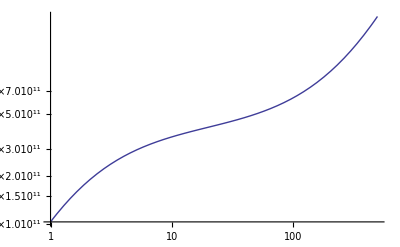

```mathematica
LogLogPlot[s[m],{m,1,500}]
```

```mathematica
x[a_,b_]:=a^2/b^2;
y[x_,b_]:=x^2/b^2;
z[x_,y_]:=x+y
```

```mathematica
z[x[1,2],y[x[1,2],2]]
az
```

z[x[1,2],y[x[1,2],2]]

0.000547134 (((24/25+0.0023[900,100]) ArcTanh[(√(576/625-52/25 0.0023[900,100]+(0.0023[900,100])^2))/(-24/25+0.0023[900,100])])/(√(576/625-52/25 0.0023[900,100]+(0.0023[900,100])^2))+1/2 Log[1/(25 0.0023[900,100])])-0.0136784 ((0.0023[900,100] ArcTanh[(√(-4 0.0023[900,100]+(0.0023[900,100])^2))/(0.0023[900,100])])/(√(-4 0.0023[900,100]+(0.0023[900,100])^2))+1/2 Log[1/(0.0023[900,100])])